```mathematica
NMAX=21; 
SetDirectory[NotebookDirectory[]];
```

## Make basis for harmonic polynomials "Run Section"

```mathematica
PrependTo[$Path,FileNameJoin[{$HomeDirectory,"Documents","Doktorarbeit","linuxfiles","Mathematica","SmatrixScripts"}]];
SetDirectory[NotebookDirectory[]];
Get["./Ypolynom_unrotated.mx"]
Get["./NormFactor_unrotated.mx"];
```

## Spherical+Radial Definitions "Run Section"

```mathematica
couple[nA_,nB_,nResult_]:=If[EvenQ[nA+nB-nResult]&&(nA+nB-nResult≥0)&&(nA+nB-nResult≤2Min[nA,nB]),1,0]
```

```mathematica
p[x_,a_,n_]:=Sum[(-1)^p Gamma[n+a+3/2]/Gamma[n+p+3/2] Binomial[a,p] x^p,{p,0,a}]
```

```mathematica
Clear[IntGauss1,IntGauss2, IntGauss4]
```

```mathematica
(*IntDirections[nn_,mm_,pp_]:=If[OddQ[nn]||OddQ[mm]||OddQ[pp],0,4π((nn-1)!!(mm-1)!!(pp-1)!!)/((nn+mm+pp+1)!!)];*)
DeltaValues[list_]:=Block[{a=list⟦1⟧,b=list⟦2⟧,c=list⟦3⟧},
If[OddQ[a]||OddQ[b]||OddQ[c],0,Multinomial[a/2,b/2,c/2]/Multinomial[a,b,c]]
];

IntDirections[nn_,mm_,pp_]:=If[OddQ[nn]||OddQ[mm]||OddQ[pp],0,4 sqrPiInv^-2 DeltaValues[{nn,mm,pp}]/(nn+mm+pp+1)]; 

IntGauss4[nn_]:=IntGauss4[nn]=sqrPiInv^-1 2^(2nn+1)/2 Gamma[1/2+nn]/√π(*/. {√π -> sqrPiInv^-1, π -> sqrPiInv^-2}*); (* ∫_0^∞ a^(2nn)Exp[-a^2/4]ⅆa *)
IntGauss2[nn_]:=IntGauss2[nn]=sqrPiInv^-1 2^(nn+1/2)/2 Gamma[1/2+nn]/√π(*/. {√π -> sqrPiInv^-1, π -> sqrPiInv^-2}*);(*√(π/2)(2nn-1)!!*); (* ∫_0^∞ a^(2nn)Exp[-a^2/2]ⅆa *)
IntGauss1[nn_]:=IntGauss1[nn]=sqrPiInv^-1 1/2 Gamma[1/2+nn]/√π(*/. {√π -> sqrPiInv^-1, π -> sqrPiInv^-2};(*(√π(2nn-1)!!)/2^(nn+1)*)*); (* ∫_0^∞ a^(2nn)Exp[-a^2]ⅆa *)
```

```mathematica
ψProjA[Cx_,Cy_,Cz_,n_,l_,a_]:=p[(Cx^2+Cy^2+Cz^2)/2,a,n]Ypolynom⟦n+1⟧⟦n+l+1⟧/.{x1->Cx,y1->Cy,z1->Cz};
ψExpA[Cx_,Cy_,Cz_,n_,l_,a_,α_]:=α p[(Cx^2+Cy^2+Cz^2)/2,a,n]Ypolynom⟦n+1⟧⟦n+l+1⟧/.{x1->Cx,y1->Cy,z1->Cz};
```

```mathematica
ψProjA[Cx,Cy,Cz,4,3,2]
```

(-Cx^3 Cz+3 Cx Cy^2 Cz) (143/4-13/2 (Cx^2+Cy^2+Cz^2)+1/4 (Cx^2+Cy^2+Cz^2)^2)

```mathematica
(*NormψA[n,l,a]:=(a!Gamma[n+a+3/2])/Gamma[n+3/2](NormFactor⟦n+1⟧⟦n+1+l⟧)^2*) (*If[deg==0, NormAIDX0⟦a+1⟧, 1] NormFactor⟦deg+1⟧;*)
```

```mathematica
(*Apparently, calling a function alone takes up a lot of time [see below], therefore, for Andrea's basis we shall from now on use ψPA and ψEA. These Basis functions are already streamlined and need to be multiplied by ψFactor[n,l,a]/(√NormψA[a,n]) to be normalized*)
NNMAX = 20;
Do[
Do[
Do[
ψPA[Cx_,Cy_,Cz_,n,l,a]=Expand[p[(Cx^2+Cy^2+Cz^2)/2,a,n]Ypolynom⟦n+1⟧⟦n+l+1⟧/.{x1->Cx,y1->Cy,z1->Cz}];
ψEA[Cx_,Cy_,Cz_,n,l,a,α_]=Expand[α p[(Cx^2+Cy^2+Cz^2)/2,a,n]Ypolynom⟦n+1⟧⟦n+l+1⟧/.{x1->Cx,y1->Cy,z1->Cz}];
ψFactor[n,l] = NormFactor⟦n+1⟧⟦n+1+l⟧;
NormψA[a,n]=(a!Gamma[n+a+3/2])/Gamma[n+3/2];

,{a,0,(NNMAX-n)/2}]
,{l,-n,n}]
,{n,0,NNMAX}]
```

```mathematica
(2! Gamma[0+2+3/2])/Gamma[0+3/2]
```

15/2

```mathematica
ψPA[x,y,z,0,0,1]
```

3/2-x^2/2-y^2/2-z^2/2

```mathematica
ψFactor[1,1] 
NormψA[0,1]
```

1

1

```mathematica
ψNormalizedA[Cx_,Cy_,Cz_,n_,l_,a_]:=ψFactor[n,l] ψPA[Cx,Cy,Cz,n,l,a]/Sqrt[NormψA[a,n]]
```

## Define general index maps "Run Section"

#### The Theory will be a vector like {2,1,1,0,0}, giving for each entry the maximal a

```mathematica
generateGetIDX[theory_] := Block[{NN=0,idx=0},
Do[
Do[
Do[
getIDX[NN,a,l] = idx;
idx=idx+1;
,{l,-NN,NN}];
,{a,0,amax}];
NN=NN+1;
,{amax,theory}];
];
generateGetIDXfull10[] := Block[{NN=0,idx=0,theory={10,9,9,8,8,7,7,6,6,5,5,4,4,3,3,2,2,1,1,0,0}},
Do[
Do[
Do[
getIDXfull10[NN,a,l] = idx;
idx=idx+1;
,{l,-NN,NN}];
,{a,0,amax}];
NN=NN+1;
,{amax,theory}];
];
generateGetIDXfull10[];
generateReferenceMapToFull10[theory_] := Block[{NN=0,idx=0},

Clear[getReferenceToFull10];
Do[
Do[
Do[
getReferenceToFull10[idx] = getIDXfull10[NN,a,l];
idx=idx+1;
,{l,-NN,NN}];
,{a,0,amax}];
NN=NN+1;
,{amax,theory}];
];
generateIDXset[theory_] := Block[{NN=0,idx=0, IDXset={}},
Clear[getIDX];
generateGetIDX[theory];
Do[
Do[
Do[
AppendTo[IDXset,{NN,a,l}];
,{l,-NN,NN}];
,{a,0,amax}];
NN=NN+1;
,{amax,theory}];
IDXset
];
(*theory⟦n⟧ = amax[n], Length[theory] = NMAX, Max[theory]=AMAX*)
(*e.g. theory = {3,3,2,2,1}; *)
(*From the chosen theory get all combinations that contribute to the full sum∑_(b=0)^AMAX ∑_(c=0)^AMAX ∑_(n1=0)^NMAX ∑_(n2=0)^NMAX for each tuple (n,a).*)
```

## Test function shift "Run Section"

```mathematica
p0[vz_]=((vz+1)^10 );
(*densitydist [vx_,vy_,vz_]=  Exp[-((vx )^2 + vy^2 + (vz+1)^2)/2]((p0[vz]));*)
densitydist[vx_,vy_,vz_] =1/(2 π^(3/2)) (Exp[-((vz + Sqrt[3/2])^2 + vy^2 + vx^2)]+ Exp[-((vz - Sqrt[3/2])^2 + vy^2 + vx^2)]);
ρ0 = Integrate[ densitydist[vx,vy,vz],{vx,-Infinity, Infinity},{vy,-Infinity, Infinity},{vz,-Infinity, Infinity}];
vmean=Integrate[ ({vx,vy,vz})densitydist[vx,vy,vz]/ρ0,{vx,-Infinity, Infinity},{vy,-Infinity, Infinity},{vz,-Infinity, Infinity}];
f0[vx_,vy_,vz_] = densitydist[vx+vmean[[1]],vy+vmean[[2]],vz+vmean[[3]]]/(ρ0);
kk=Integrate[ ( 1/3 (vx^2+vy^2+vz^2))f0[vx,vy,vz],{vx,-Infinity, Infinity},{vy,-Infinity, Infinity},{vz,-Infinity, Infinity}];
ff0[vx_,vy_,vz_]=kk^(3/2)densitydist[kk^(1/2)(vx)+vmean[[1]],kk^(1/2)(vy)+vmean[[2]],kk^(1/2)(vz)+vmean[[3]]]/ρ0;

kkA=Integrate[ ( 1/3 ((vx-vmean[[1]])^2+(vy-vmean[[2]])^2+(vz-vmean[[3]])^2))/(ρ0) densitydist[vx,vy,vz],{vx,-Infinity, Infinity},{vy,-Infinity, Infinity},{vz,-Infinity, Infinity}];
```

```mathematica
N[densitydist[0,0,0]]
```

0.0400713

```mathematica
N[ Sqrt[3/2]]
```

1.22474

```mathematica
vmean
```

{0,0,0}

```mathematica
N[densitydist[1,1,1]]
```

0.0116398

```mathematica
kk
```

1

```mathematica
kkA
```

1

```mathematica
Integrate[ densitydist[vx,vy,vz],{vx,-Infinity, Infinity},{vy,-Infinity, Infinity},{vz,-Infinity, Infinity}];
```

```mathematica
1890 √2 π^(3/2)
```

1890 √2 π^(3/2)

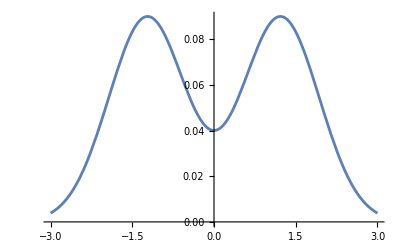

```mathematica
Plot[ff0[0,0,vz],{vz,-3,3}]
```

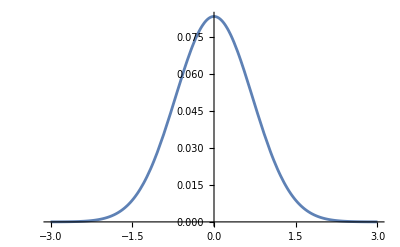

```mathematica
Plot[ff0[0,vy,1.5],{vy,-3,3}]
```

```mathematica
Integrate[ ( 1/3 (vx^2+vy^2+vz^2))ff0[vx,vy,vz],{vx,-Infinity, Infinity},{vy,-Infinity, Infinity},{vz,-Infinity, Infinity}]
```

1

```mathematica
Integrate[ 1/3(((vx-vmean[[1]])/kk^(1/2))^2+((vy-vmean[[2]])/kk^(1/2))^2+((vz-vmean[[3]])/kk^(1/2))^2)/ρ0 densitydist[vx,vy,vz],{vx,-Infinity, Infinity},{vy,-Infinity, Infinity},{vz,-Infinity, Infinity}]
```

1

```mathematica
Clear[a,b,c]
```

```mathematica
Integrate[ ( vx^2+vy^7+vz^3 )ff0[vx,vy,vz],{vx,-Infinity, Infinity},{vy,-Infinity, Infinity},{vz,-Infinity, Infinity}]
```

1/2

```mathematica
Integrate[ (( ((vx-vmean[[1]])/kk^(1/2))^2+((vy-vmean[[2]])/kk^(1/2))^7+((vz-vmean[[3]])/kk^(1/2))^3) )/(ρ0)densitydist[vx,vy,vz],{vx,-Infinity, Infinity},{vy,-Infinity, Infinity},{vz,-Infinity, Infinity}]
```

1/2

## Test Normalization of chosen Scalar product <p,q> :=Sqrt[(2π)^3]^1∫ p[v] q[v] e^(-c^2)ⅆv "Run Section"

```mathematica
(*This is the integral we want to solve for many different combinations of two sets of (n,l,a)
 Unfortunately, its evaluation takes a fairly long time*)
Integrate[ (1/(Sqrt[2π])^3) ψPA[vx,vy,vz,2,2,1]ψPA[vx,vy,vz,2,2,1]Exp[-((vx )^2 + (vy)^2 + (vz)^2)/2],{vx,-Infinity, Infinity},{vy,-Infinity, Infinity},{vz,-Infinity, Infinity}]
```

14

```mathematica
(*We will now make this evaluation faster. 
Step 1: Get analytical replacement rule for the integral of a monomial multiplied with the gaussian*)
Clear[a,b,c]
Integrate[ (1/(Sqrt[2π])^3) ( vx^a vy^b vz^c )Exp[-((vx )^2 + (vy)^2 + (vz)^2)/2],{vx,-Infinity, Infinity},{vy,-Infinity, Infinity},{vz,-Infinity, Infinity}]
```

ConditionalExpression[(2^(1/2 (-1+a)+1/2 (-5+b+c)) (1+(-1)^a) (1+(-1)^b) (1+(-1)^c) Gamma[(1+a)/2] Gamma[(1+b)/2] Gamma[(1+c)/2])/π^(3/2), Re[a]>-1]

```mathematica
(* Step 2: Copy the above expression and simplify it knowing that a,b,c will be zero or whole numbers:*)
getMonomialCoefficient[a_,b_,c_]:=If[EvenQ[a] && EvenQ[b] && EvenQ[c],(2^(1/2 (-6+a+b+c)) (2) (2) (2) Gamma[(1+a)/2] Gamma[(1+b)/2] Gamma[(1+c)/2])/π^(3/2),0];
```

```mathematica
(* Step 3: Define a function, that uses the above expression for monomials and multiplies them with a fitting set of normalization coefficients:*)
getBasisproductWeight[a_,n_,l_,b_,n1_,l1_]:=ψFactor[n,l]ψFactor[n1,l1]Total[CoefficientRules[ψPA[vx,vy,vz,n,l,a]ψPA[vx,vy,vz,n1,l1,b],{vx,vy,vz}]/. Rule[{aa_,bb_,cc_},factor_] :>  factor getMonomialCoefficient[aa,bb,cc]]/(Sqrt[NormψA[a,n]]Sqrt[NormψA[b,n1]])
```

```mathematica
(*Step 4: The actual test - we expect an identity matrix, if the normalization is correct
 You can obviously choose a larger nmax and also define different nmin*)
nmin=9;
nmax=11;
MatrixForm[Flatten[Table[
Flatten[Table[
(*{getBasisproductWeight[a,n,l,b,n1,l1],{a,n,l},{b,n1,l1}}*)
getBasisproductWeight[a,n,l,b,n1,l1]
,{n,nmin,nmax},{a,0,(nmax-n)/2},{l,-n,n}],2]
,{n1,nmin,nmax},{b,0,(nmax-n1)/2},{l1,-n1,n1}],2]]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

## Get projection Rules ∫ Psi[v] f[v] ⅆv "Run Section"

```mathematica
Clear[a,b,c]
```

```mathematica
Integrate[ ( vx^a vy^b vz^c )ff0[vx,vy,vz],{vx,-Infinity, Infinity},{vy,-Infinity, Infinity},{vz,-Infinity, Infinity}]
```

∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ vx^a vy^b vz^c ff0[vx,vy,vz]ⅆvzⅆvyⅆvx

```mathematica
(2^(1/2+a/2+1/2 (5+b+c)) 3^(1/2+a/2+1/2 (-7+b+c)) 13^(-1/2-a/2+1/2 (1-b-c)) (2) (2) Gamma[(3+a)/2] Gamma[(1+b)/2] Gamma[(11+c)/2] (2))/(35 (1+a) π^(3/2))
```

(2^(7/2+a/2+1/2 (5+b+c)) 3^(1/2+a/2+1/2 (-7+b+c)) 13^(-1/2-a/2+1/2 (1-b-c)) Gamma[(3+a)/2] Gamma[(1+b)/2] Gamma[(11+c)/2])/(35 (1+a) π^(3/2))

```mathematica
(*getProjectionCoeff[a_,b_,c_]=((1+(-1)^a) (1+(-1)^b) (1+(-1)^c) Gamma[(1+a)/2] Gamma[(1+b)/2] Gamma[(1+c)/2] Hypergeometric1F1[-a/2,1/2,-3/2])/(8 π^(3/2));*)
Clear[getProjectionCoeff,getProjectionWeight];
```

```mathematica
getProjectionCoeff[a_,b_,c_]:=If[EvenQ[a] && EvenQ[b] && EvenQ[c],(2^(1/2+a/2+1/2 (5+b+c)) 3^(1/2+a/2+1/2 (-7+b+c)) 13^(-1/2-a/2+1/2 (1-b-c)) (2) (2) Gamma[(3+a)/2] Gamma[(1+b)/2] Gamma[(11+c)/2] (2))/(35 (1+a) π^(3/2)),0]
```

```mathematica
getProjectionWeight[a_,n_,l_]:=If[EvenQ[n],ψFactor[n,l]Total[CoefficientRules[ψProjA[vx,vy,vz,n,l,a],{vx,vy,vz}]/. Rule[{aa_,bb_,cc_},factor_] :>  factor getProjectionCoeff[aa,bb,cc]]/Sqrt[NormψA[a,n]],0]
```

```mathematica
∫Psi[v]ff[v] ⅆv
```

∫ff[v] Psi[v]ⅆv

```mathematica
Integral[f[x],{x,-1,1}]
```

Integral[f[x],{x,-1,1}]

## Define generation of the text file "Run Section"

```mathematica
generatefFile[theory_,filename_] :=Block[{file,sText, IDXset,idx,NN,a,l, factor},
If[FileExistsQ[filename], DeleteFile[filename]
];
file=File[CreateFile[filename]];

sText="// This code has been generated automatically using the Mathematica file C++CodeGenerator.nb
// This file calculates moments from a distribution
// Author: Anja Matena (anja.matena@rwth-aachen.de)

#include <cstddef>
#include <cmath>
#include <math.h>
#include <algorithm>
#include <vector>

#include <dergeraet/config.hpp>

template <typename real, size_t order>
void eval_moments( size_t n, size_t l, const real *coeffs, const config_t<real> &conf, real* moments )
{
	const size_t k   = l   / (conf.Nx * conf.Ny); 
	const size_t tmp = l   % (conf.Nx * conf.Ny);
	const size_t j   = tmp / conf.Nx;
	const size_t i   = tmp % conf.Nx;

	const real x = conf.x_min + i*conf.dx;
	const real y = conf.y_min + j*conf.dy;
	const real z = conf.z_min + k*conf.dz;

	const real du = (conf.u_max-conf.u_min) / conf.Nu; 
	const real dv = (conf.v_max-conf.v_min) / conf.Nv;
	const real dw = (conf.w_max-conf.w_min) / conf.Nw;

	const real u_min = conf.u_min + 0.5*du;
	const real v_min = conf.v_min + 0.5*dv;
	const real w_min = conf.w_min + 0.5*dw;

	real rho = 0;
	real j_x = 0;
	real j_y = 0;
	real j_z = 0;
	real std_dev = 0;

	std::vector<std::vector<std::vector<real>>> f(conf.Nu, std::vector<std::vector<real>>(conf.Nv, std::vector<real>(conf.Nw)));

	for ( size_t kk = 0; kk < conf.Nw; ++kk )
	for ( size_t jj = 0; jj < conf.Nv; ++jj )
	for ( size_t ii = 0; ii < conf.Nu; ++ii )
	{
		real u = u_min + ii*du;
		real v = v_min + jj*dv;
		real w = w_min + kk*dw;
		real func = eval_f<real,order>( n, x, y, z, u, v, w, coeffs, conf );

		rho += func * du * dv * dw;
		j_x += func * u * du * dv * dw;
		j_y += func * v * du * dv * dw;
		j_z += func * w * du * dv * dw;

		f[ii][jj][kk] = func;
	}

	// Calculate vmean
	j_x /= rho;
	j_y /= rho;
	j_z /= rho;

	// Calculate standard deviation
	for ( size_t kk = 0; kk < conf.Nw; ++kk )
	for ( size_t jj = 0; jj < conf.Nv; ++jj )
	for ( size_t ii = 0; ii < conf.Nu; ++ii )
	{
		// vmean = 0
		real unew = u_min + ii*du - j_x;
		real vnew = v_min + jj*dv - j_y;
		real wnew = w_min + kk*dw - j_z;

		std_dev += f[ii][jj][kk] * 1/3 * (pow(unew, 2) + pow(vnew, 2) + pow(wnew, 2)) * du * dv * dw;
	}

	std_dev = sqrt(std_dev / rho); // Standard deviation

	if(rho < pow(10,-6)) {
		for (int i = 0; i < ";

IDXset=generateIDXset[theory];
sText = sText <> ToString[Length[IDXset]] <> "; i++) {
			moments[i] = 0;
		}
	} else {

		// Calculate moments
		for ( size_t kk = 0; kk < conf.Nw; ++kk )
		for ( size_t jj = 0; jj < conf.Nv; ++jj )
		for ( size_t ii = 0; ii < conf.Nu; ++ii )
		{
			// std_dev = 1
			real unew = (u_min + ii*du - j_x)/std_dev;
			real vnew = (v_min + jj*dv - j_y)/std_dev;
			real wnew = (w_min + kk*dw - j_z)/std_dev;

";
Do[
{NN,a,l}=IDXset[[idx]];
factor = StringReplace[ToString[CForm[N[ψNormalizedA[unew,vnew,wnew,NN,l,a]]]], "Power" -> "pow"];
sText=sText<>"\t\t\tmoments["<>ToString[idx-1]<>"] += f[ii][jj][kk]/rho * du * dv * dw * "<> ToString[factor]<>"; \n";
,{idx,Length[IDXset]}];


sText = sText <> "\t\t}
	}
";
sText=sText<>"\tmoments["<>ToString[Length[IDXset]]<>"] = rho" <>"; \n";
sText=sText<>"\tmoments["<>ToString[Length[IDXset]+1]<>"] = j_x" <>"; \n";
sText=sText<>"\tmoments["<>ToString[Length[IDXset]+2] <>"] = j_y" <>"; \n";
sText=sText<>"\tmoments["<>ToString[Length[IDXset]+3] <>"] = j_z" <>"; \n";
sText=sText<>"\tmoments["<>ToString[Length[IDXset]+4] <>"] = std_dev" <>"; \n";
sText = sText <> "} 
";

sText = sText <> "template <typename real, size_t order>
real pi_inverse( real u, real v, real w, real* moments )
{
	real value = 0;
	u = (u - ";

sText=sText<>"moments["<>ToString[Length[IDXset]+1] <>"]) / " <> "moments[" <>ToString[Length[IDXset]+4]<>"]" <>"; \n";
sText=sText<>"\tv = (v - moments["<> ToString[Length[IDXset]+2] <>"]) / " <> "moments[" <>ToString[Length[IDXset]+4]<>"]" <>"; \n";
sText=sText<>"\tw = (w - moments["<>ToString[Length[IDXset]+3] <>"]) / " <> "moments[" <>ToString[Length[IDXset]+4]<>"]" <>"; \n";
Do[
{NN,a,l}=IDXset[[idx]];
factor = StringReplace[ToString[CForm[N[ψNormalizedA[u,v,w,NN,l,a]]]], "Power" -> "pow"];
sText=sText<>"\tvalue += moments["<>ToString[idx-1]<>"] * exp(-(pow(u,2) + pow(v,2) + pow(w,2))/2) * "<> ToString[factor]<>"; \n";
,{idx,Length[IDXset]}];

sText = sText <> "\tvalue *= moments["<>ToString[Length[IDXset]]<>"]/pow(moments[" <> ToString[Length[IDXset]+4] <>"],3) * 0.06349363593424097;\n";

sText = sText <> "\treturn value;
}
";

StringTrim[sText] (*<> "\n"*);
WriteLine[file,sText];
Close[file];
];

N[1/(Sqrt[2π])^3]
```

0.0634936

## Generate the text files "Run Section"

```mathematica
NotebookDirectory[]
```

/Users/amat/Documents/Privat/Uni/Semester5/ACoM/dergeraet/AnjaMathematica/

```mathematica
distname="CalculateMoments"
```

CalculateMoments

```mathematica
theory={2,1,1,0,0};
(*theory = {10};*)
generatefFile[theory,NotebookDirectory[] <>distname<>"_Full2" <> ".cpp"]
```

```mathematica
"// This code has been generated automatically using the Mathematica file C++CodeGenerator.nb\\n// This file calculates moments from a distribution\\n// Author: Anja Matena (anja.matena@rwth-aachen.de)\\ntemplate <typename real, size_t order>\\nvoid eval_rho( size_t n, size_t l, const real *coeffs, const config_t<real> &conf, real* moments )\\n{ \\n    const size_t k   = l   / (conf.Nx * conf.Ny); \\n    const size_t tmp = l   % (conf.Nx * conf.Ny);\\n    const size_t j   = tmp / conf.Nx;\\n    const size_t i   = tmp % conf.Nx;\\n\\n    const real x = conf.x_min + i*conf.dx;\\n    const real y = conf.y_min + j*conf.dy;\\n    const real z = conf.z_min + k*conf.dz;\\n\\n    const real du = (conf.u_max-conf.u_min) / conf.Nu; \\n    const real dv = (conf.v_max-conf.v_min) / conf.Nv;\\n    const real dw = (conf.w_max-conf.w_min) / conf.Nw;\\n\\n    const real u_min = conf.u_min + 0.5*du;\\n    const real v_min = conf.v_min + 0.5*dv;\\n    const real w_min = conf.w_min + 0.5*dw;\\n\\t\\n    real rho = 0;\\n    real j_x = 0;\\n    real j_y = 0;\\n    real j_z = 0;\\n    real std_dev = 0;\\n\\n    for ( size_t kk = 0; kk < conf.Nw; ++kk )\\n    for ( size_t jj = 0; jj < conf.Nv; ++jj )\\n    for ( size_t ii = 0; ii < conf.Nu; ++ii )\\n    {\\n        real u = u_min + ii*du;\\n        real v = v_min + jj*dv;\\n        real w = w_min + kk*dw;\\n        real f = eval_f<real,order>( n, x, y, z, u, v, w, coeffs, conf );\\n        \\n        rho += f;\\n        j_x += f*u;\\n        j_y += f*v;\\n        j_z += f*w;\\n    }\\n\\n    // Calculate vmean\\n    j_x /= rho;\\n    j_y /= rho;\\n    j_z /= rho;\\n\\n    // Calculate standard deviation\\n    for ( size_t kk = 0; kk < conf.Nw; ++kk )\\n    for ( size_t jj = 0; jj < conf.Nv; ++jj )\\n    for ( size_t ii = 0; ii < conf.Nu; ++ii )\\n    {\\n        real u = u_min + ii * du;\\n        real v = v_min + jj * dv;\\n        real w = w_min + kk * dw;\\n        real f = eval_f<real,order>( n, x, y, z, u, v, w, coeffs, conf );\\n\\t\\t\\n        // vmean = 0\\n        real unew = u - j_x;\\n        real vnew = v - j_y;\\n        real wnew = w - j_z;\\n        \\n        std_dev += f * (pow(unew, 2) + pow(v_new, 2) + pow(w_new, 2));\\n    }\\n\\n    std_dev = sqrt(std_dev / rho); // Standard deviation\\n\\n    // Calculate moments\\n    for ( size_t kk = 0; kk < conf.Nw; ++kk )\\n    for ( size_t jj = 0; jj < conf.Nv; ++jj )\\n    for ( size_t ii = 0; ii < conf.Nu; ++ii )\\n    {\\n        u = u_min + ii*du;\\n        v = v_min + jj*dv;\\n        w = w_min + kk*dw;\\n        f = eval_f<real,order>( n, x, y, z, u, v, w, coeffs, conf );\\n\\n\\t\\t\\n        // std_dev = 1\\n        unew (u - j_x)/std_dev;\\n        vnew = (v - j_y)/std_dev;\\n        wnew = (w - j_z)/std_dev;\\n     \\n\\tmoments[0] += f* 1; \\n\\tmoments[1] += f* 1.5 + (-Power(unew,2) - Power(vnew,2) - Power(wnew,2))/2.; \\n\\tmoments[2] += f* 3.75 - (5*(Power(unew,2) + Power(vnew,2) + Power(wnew,2)))/2. + Power(Power(unew,2) + Power(vnew,2) + Power(wnew,2),2)/4.; \\n\\tmoments[3] += f* vnew; \\n\\tmoments[4] += f* wnew; \\n\\tmoments[5] += f* -unew; \\n\\tmoments[6] += f* vnew*(2.5 + (-Power(unew,2) - Power(vnew,2) - Power(wnew,2))/2.); \\n\\tmoments[7] += f* wnew*(2.5 + (-Power(unew,2) - Power(vnew,2) - Power(wnew,2))/2.); \\n\\tmoments[8] += f* -(unew*(2.5 + (-Power(unew,2) - Power(vnew,2) - Power(wnew,2))/2.)); \\n\\tmoments[9] += f* unew*vnew; \\n\\tmoments[10] += f* vnew*wnew; \\n\\tmoments[11] += f* -Power(unew,2) - Power(vnew,2) + 2*Power(wnew,2); \\n\\tmoments[12] += f* -(unew*wnew); \\n\\tmoments[13] += f* Power(unew,2) - Power(vnew,2); \\n\\tmoments[14] += f* unew*vnew*(3.5 + (-Power(unew,2) - Power(vnew,2) - Power(wnew,2))/2.); \\n\\tmoments[15] += f* vnew*wnew*(3.5 + (-Power(unew,2) - Power(vnew,2) - Power(wnew,2))/2.); \\n\\tmoments[16] += f* (-Power(unew,2) - Power(vnew,2) + 2*Power(wnew,2))*(3.5 + (-Power(unew,2) - Power(vnew,2) - Power(wnew,2))/2.); \\n\\tmoments[17] += f* -(unew*wnew*(3.5 + (-Power(unew,2) - Power(vnew,2) - Power(wnew,2))/2.)); \\n\\tmoments[18] += f* (Power(unew,2) - Power(vnew,2))*(3.5 + (-Power(unew,2) - Power(vnew,2) - Power(wnew,2))/2.); \\n\\tmoments[19] += f* 3*Power(unew,2)*vnew - Power(vnew,3); \\n\\tmoments[20] += f* unew*vnew*wnew; \\n\\tmoments[21] += f* -(Power(unew,2)*vnew) - Power(vnew,3) + 4*vnew*Power(wnew,2); \\n\\tmoments[22] += f* -3*Power(unew,2)*wnew - 3*Power(vnew,2)*wnew + 2*Power(wnew,3); \\n\\tmoments[23] += f* Power(unew,3) + unew*Power(vnew,2) - 4*unew*Power(wnew,2); \\n\\tmoments[24] += f* Power(unew,2)*wnew - Power(vnew,2)*wnew; \\n\\tmoments[25] += f* -Power(unew,3) + 3*unew*Power(vnew,2); \\n\\tmoments[26] += f* Power(unew,3)*vnew - unew*Power(vnew,3); \\n\\tmoments[27] += f* 3*Power(unew,2)*vnew*wnew - Power(vnew,3)*wnew; \\n\\tmoments[28] += f* -(Power(unew,3)*vnew) - unew*Power(vnew,3) + 6*unew*vnew*Power(wnew,2); \\n\\tmoments[29] += f* -3*Power(unew,2)*vnew*wnew - 3*Power(vnew,3)*wnew + 4*vnew*Power(wnew,3); \\n\\tmoments[30] += f* 3*Power(unew,4) + 6*Power(unew,2)*Power(vnew,2) + 3*Power(vnew,4) - 24*Power(unew,2)*Power(wnew,2) - 24*Power(vnew,2)*Power(wnew,2) + 8*Power(wnew,4); \\n\\tmoments[31] += f* 3*Power(unew,3)*wnew + 3*unew*Power(vnew,2)*wnew - 4*unew*Power(wnew,3); \\n\\tmoments[32] += f* -Power(unew,4) + Power(vnew,4) + 6*Power(unew,2)*Power(wnew,2) - 6*Power(vnew,2)*Power(wnew,2); \\n\\tmoments[33] += f* -(Power(unew,3)*wnew) + 3*unew*Power(vnew,2)*wnew; \\n\\tmoments[34] += f* Power(unew,4) - 6*Power(unew,2)*Power(vnew,2) + Power(vnew,4); \\n   }\\n    rho = 1 - du*dv*dw*rho;\\n    moments /= rho; \\n}"
```

// This code has been generated automatically using the Mathematica file C++CodeGenerator.nb\n// This file calculates moments from a distribution\n// Author: Anja Matena (anja.matena@rwth-aachen.de)\ntemplate <typename real, size_t order>\nvoid eval_rho( size_t n, size_t l, const real *coeffs, const config_t<real> &conf, real* moments )\n{ \n    const size_t k   = l   / (conf.Nx * conf.Ny); \n    const size_t tmp = l   % (conf.Nx * conf.Ny);\n    const size_t j   = tmp / conf.Nx;\n    const size_t i   = tmp % conf.Nx;\n\n    const real x = conf.x_min + i*conf.dx;\n    const real y = conf.y_min + j*conf.dy;\n    const real z = conf.z_min + k*conf.dz;\n\n    const real du = (conf.u_max-conf.u_min) / conf.Nu; \n    const real dv = (conf.v_max-conf.v_min) / conf.Nv;\n    const real dw = (conf.w_max-conf.w_min) / conf.Nw;\n\n    const real u_min = conf.u_min + 0.5*du;\n    const real v_min = conf.v_min + 0.5*dv;\n    const real w_min = conf.w_min + 0.5*dw;\n\t\n    real rho = 0;\n    real j_x = 0;\n    real j_y = 0;\n    real j_z = 0;\n    real std_dev = 0;\n\n    for ( size_t kk = 0; kk < conf.Nw; ++kk )\n    for ( size_t jj = 0; jj < conf.Nv; ++jj )\n    for ( size_t ii = 0; ii < conf.Nu; ++ii )\n    {\n        real u = u_min + ii*du;\n        real v = v_min + jj*dv;\n        real w = w_min + kk*dw;\n        real f = eval_f<real,order>( n, x, y, z, u, v, w, coeffs, conf );\n        \n        rho += f;\n        j_x += f*u;\n        j_y += f*v;\n        j_z += f*w;\n    }\n\n    // Calculate vmean\n    j_x /= rho;\n    j_y /= rho;\n    j_z /= rho;\n\n    // Calculate standard deviation\n    for ( size_t kk = 0; kk < conf.Nw; ++kk )\n    for ( size_t jj = 0; jj < conf.Nv; ++jj )\n    for ( size_t ii = 0; ii < conf.Nu; ++ii )\n    {\n        real u = u_min + ii * du;\n        real v = v_min + jj * dv;\n        real w = w_min + kk * dw;\n        real f = eval_f<real,order>( n, x, y, z, u, v, w, coeffs, conf );\n\t\t\n        // vmean = 0\n        real unew = u - j_x;\n        real vnew = v - j_y;\n        real wnew = w - j_z;\n        \n        std_dev += f * (pow(unew, 2) + pow(v_new, 2) + pow(w_new, 2));\n    }\n\n    std_dev = sqrt(std_dev / rho); // Standard deviation\n\n    // Calculate moments\n    for ( size_t kk = 0; kk < conf.Nw; ++kk )\n    for ( size_t jj = 0; jj < conf.Nv; ++jj )\n    for ( size_t ii = 0; ii < conf.Nu; ++ii )\n    {\n        u = u_min + ii*du;\n        v = v_min + jj*dv;\n        w = w_min + kk*dw;\n        f = eval_f<real,order>( n, x, y, z, u, v, w, coeffs, conf );\n\n\t\t\n        // std_dev = 1\n        unew (u - j_x)/std_dev;\n        vnew = (v - j_y)/std_dev;\n        wnew = (w - j_z)/std_dev;\n     \n\tmoments[0] += f* 1; \n\tmoments[1] += f* 1.5 + (-Power(unew,2) - Power(vnew,2) - Power(wnew,2))/2.; \n\tmoments[2] += f* 3.75 - (5*(Power(unew,2) + Power(vnew,2) + Power(wnew,2)))/2. + Power(Power(unew,2) + Power(vnew,2) + Power(wnew,2),2)/4.; \n\tmoments[3] += f* vnew; \n\tmoments[4] += f* wnew; \n\tmoments[5] += f* -unew; \n\tmoments[6] += f* vnew*(2.5 + (-Power(unew,2) - Power(vnew,2) - Power(wnew,2))/2.); \n\tmoments[7] += f* wnew*(2.5 + (-Power(unew,2) - Power(vnew,2) - Power(wnew,2))/2.); \n\tmoments[8] += f* -(unew*(2.5 + (-Power(unew,2) - Power(vnew,2) - Power(wnew,2))/2.)); \n\tmoments[9] += f* unew*vnew; \n\tmoments[10] += f* vnew*wnew; \n\tmoments[11] += f* -Power(unew,2) - Power(vnew,2) + 2*Power(wnew,2); \n\tmoments[12] += f* -(unew*wnew); \n\tmoments[13] += f* Power(unew,2) - Power(vnew,2); \n\tmoments[14] += f* unew*vnew*(3.5 + (-Power(unew,2) - Power(vnew,2) - Power(wnew,2))/2.); \n\tmoments[15] += f* vnew*wnew*(3.5 + (-Power(unew,2) - Power(vnew,2) - Power(wnew,2))/2.); \n\tmoments[16] += f* (-Power(unew,2) - Power(vnew,2) + 2*Power(wnew,2))*(3.5 + (-Power(unew,2) - Power(vnew,2) - Power(wnew,2))/2.); \n\tmoments[17] += f* -(unew*wnew*(3.5 + (-Power(unew,2) - Power(vnew,2) - Power(wnew,2))/2.)); \n\tmoments[18] += f* (Power(unew,2) - Power(vnew,2))*(3.5 + (-Power(unew,2) - Power(vnew,2) - Power(wnew,2))/2.); \n\tmoments[19] += f* 3*Power(unew,2)*vnew - Power(vnew,3); \n\tmoments[20] += f* unew*vnew*wnew; \n\tmoments[21] += f* -(Power(unew,2)*vnew) - Power(vnew,3) + 4*vnew*Power(wnew,2); \n\tmoments[22] += f* -3*Power(unew,2)*wnew - 3*Power(vnew,2)*wnew + 2*Power(wnew,3); \n\tmoments[23] += f* Power(unew,3) + unew*Power(vnew,2) - 4*unew*Power(wnew,2); \n\tmoments[24] += f* Power(unew,2)*wnew - Power(vnew,2)*wnew; \n\tmoments[25] += f* -Power(unew,3) + 3*unew*Power(vnew,2); \n\tmoments[26] += f* Power(unew,3)*vnew - unew*Power(vnew,3); \n\tmoments[27] += f* 3*Power(unew,2)*vnew*wnew - Power(vnew,3)*wnew; \n\tmoments[28] += f* -(Power(unew,3)*vnew) - unew*Power(vnew,3) + 6*unew*vnew*Power(wnew,2); \n\tmoments[29] += f* -3*Power(unew,2)*vnew*wnew - 3*Power(vnew,3)*wnew + 4*vnew*Power(wnew,3); \n\tmoments[30] += f* 3*Power(unew,4) + 6*Power(unew,2)*Power(vnew,2) + 3*Power(vnew,4) - 24*Power(unew,2)*Power(wnew,2) - 24*Power(vnew,2)*Power(wnew,2) + 8*Power(wnew,4); \n\tmoments[31] += f* 3*Power(unew,3)*wnew + 3*unew*Power(vnew,2)*wnew - 4*unew*Power(wnew,3); \n\tmoments[32] += f* -Power(unew,4) + Power(vnew,4) + 6*Power(unew,2)*Power(wnew,2) - 6*Power(vnew,2)*Power(wnew,2); \n\tmoments[33] += f* -(Power(unew,3)*wnew) + 3*unew*Power(vnew,2)*wnew; \n\tmoments[34] += f* Power(unew,4) - 6*Power(unew,2)*Power(vnew,2) + Power(vnew,4); \n   }\n    rho = 1 - du*dv*dw*rho;\n    moments /= rho; \n}

```mathematica
"// This code has been generated automatically .....\\n// This file calculates moments from a distribution\\n// Author: Anja Matena (anja.matena@rwth-aachen.de)\\ntemplate <typename real, size_t order>\\nvoid eval_rho( size_t n, size_t l, const real *coeffs, const config_t<real> &conf, real* moments )\\n{ \\n    const size_t k   = l   / (conf.Nx * conf.Ny); \\n    const size_t tmp = l   % (conf.Nx * conf.Ny);\\n    const size_t j   = tmp / conf.Nx;\\n    const size_t i   = tmp % conf.Nx;\\n\\n    const real x = conf.x_min + i*conf.dx;\\n    const real y = conf.y_min + j*conf.dy;\\n    const real z = conf.z_min + k*conf.dz;\\n\\n    const real du = (conf.u_max-conf.u_min) / conf.Nu; \\n    const real dv = (conf.v_max-conf.v_min) / conf.Nv;\\n    const real dw = (conf.w_max-conf.w_min) / conf.Nw;\\n\\n    const real u_min = conf.u_min + 0.5*du;\\n    const real v_min = conf.v_min + 0.5*dv;\\n    const real w_min = conf.w_min + 0.5*dw;\\n\\t\\n\\treal rho = 0;\\n    real j_x = 0;\\n    real j_y = 0;\\n    real j_z = 0;\\n    real std_dev = 0;\\n\\n    for ( size_t kk = 0; kk < conf.Nw; ++kk )\\n    for ( size_t jj = 0; jj < conf.Nv; ++jj )\\n    for ( size_t ii = 0; ii < conf.Nu; ++ii )\\n    {\\n        real u = u_min + ii*du;\\n        real v = v_min + jj*dv;\\n        real w = w_min + kk*dw;\\n        real f = eval_f<real,order>( n, x, y, z, u, v, w, coeffs, conf );\\n        \\n        rho += f;\\n        j_x += f*u;\\n        j_y += f*v;\\n        j_z += f*w;\\n        \\n\\t}\\n\\trho = 1 - du*dv*dw*rho;\\n    // ...\\n\\n\\t// Calculate vmean\\n    j_x /= rho;\\n    j_y /= rho;\\n    j_z /= rho;\\n\\n    // vmean=0\\n    u_min -= j_x;\\n    v_min -= j_y;\\n    w_min -= j_z;\\n\\n\\t// Calculate standard deviation\\n\\tfor ( size_t kk = 0; kk < conf.Nw; ++kk )\\n    for ( size_t jj = 0; jj < conf.Nv; ++jj )\\n    for ( size_t ii = 0; ii < conf.Nu; ++ii )\\n    {\\n        real u = u_min + ii * du;\\n        real v = v_min + jj * dv;\\n        real w = w_min + kk * dw;\\n        real f = eval_f<real,order>( n, x, y, z, u, v, w, coeffs, conf );\\n        \\n        std_dev += pow(f, 2);\\n\\t}\\n\\tstd_dev = sqrt(std_dev / rho); // Standard deviation\\n\\n\\t// std_dev=1\\n    u /= std_dev;\\n    v /= std_dev;\\n    w /= std_dev;\\n\\n\\t// Calculate new rho, j_x, j_y and j_z\\n\\treal rho = 0;\\n    for ( size_t kk = 0; kk < conf.Nw * std_dev; ++kk )\\n    for ( size_t jj = 0; jj < conf.Nv * std_dev; ++jj )\\n    for ( size_t ii = 0; ii < conf.Nu * std_dev; ++ii )\\n    {\\n        real u = u_min + ii*du;\\n        real v = v_min + jj*dv;\\n        real w = w_min + kk*dw;\\n        real f = eval_f<real,order>( n, x, y, z, u, v, w, coeffs, conf );\\n        \\n        rho += f;\\n        j_x += f*u;\\n        j_y += f*v;\\n        j_z += f*w;\\n        // ...\\n\\t \\t moments[0] += f* 1; \\n\\t \\t moments[1] += f* 1.5 + (-Power(u,2) - Power(v,2) - Power(w,2))/2.; \\n\\t \\t moments[2] += f* 3.75 - (5*(Power(u,2) + Power(v,2) + Power(w,2)))/2. + Power(Power(u,2) + Power(v,2) + Power(w,2),2)/4.; \\n\\t \\t moments[3] += f* v; \\n\\t \\t moments[4] += f* w; \\n\\t \\t moments[5] += f* -u; \\n\\t \\t moments[6] += f* v*(2.5 + (-Power(u,2) - Power(v,2) - Power(w,2))/2.); \\n\\t \\t moments[7] += f* w*(2.5 + (-Power(u,2) - Power(v,2) - Power(w,2))/2.); \\n\\t \\t moments[8] += f* -(u*(2.5 + (-Power(u,2) - Power(v,2) - Power(w,2))/2.)); \\n\\t \\t moments[9] += f* u*v; \\n\\t \\t moments[10] += f* v*w; \\n\\t \\t moments[11] += f* -Power(u,2) - Power(v,2) + 2*Power(w,2); \\n\\t \\t moments[12] += f* -(u*w); \\n\\t \\t moments[13] += f* Power(u,2) - Power(v,2); \\n\\t \\t moments[14] += f* u*v*(3.5 + (-Power(u,2) - Power(v,2) - Power(w,2))/2.); \\n\\t \\t moments[15] += f* v*w*(3.5 + (-Power(u,2) - Power(v,2) - Power(w,2))/2.); \\n\\t \\t moments[16] += f* (-Power(u,2) - Power(v,2) + 2*Power(w,2))*(3.5 + (-Power(u,2) - Power(v,2) - Power(w,2))/2.); \\n\\t \\t moments[17] += f* -(u*w*(3.5 + (-Power(u,2) - Power(v,2) - Power(w,2))/2.)); \\n\\t \\t moments[18] += f* (Power(u,2) - Power(v,2))*(3.5 + (-Power(u,2) - Power(v,2) - Power(w,2))/2.); \\n\\t \\t moments[19] += f* 3*Power(u,2)*v - Power(v,3); \\n\\t \\t moments[20] += f* u*v*w; \\n\\t \\t moments[21] += f* -(Power(u,2)*v) - Power(v,3) + 4*v*Power(w,2); \\n\\t \\t moments[22] += f* -3*Power(u,2)*w - 3*Power(v,2)*w + 2*Power(w,3); \\n\\t \\t moments[23] += f* Power(u,3) + u*Power(v,2) - 4*u*Power(w,2); \\n\\t \\t moments[24] += f* Power(u,2)*w - Power(v,2)*w; \\n\\t \\t moments[25] += f* -Power(u,3) + 3*u*Power(v,2); \\n\\t \\t moments[26] += f* Power(u,3)*v - u*Power(v,3); \\n\\t \\t moments[27] += f* 3*Power(u,2)*v*w - Power(v,3)*w; \\n\\t \\t moments[28] += f* -(Power(u,3)*v) - u*Power(v,3) + 6*u*v*Power(w,2); \\n\\t \\t moments[29] += f* -3*Power(u,2)*v*w - 3*Power(v,3)*w + 4*v*Power(w,3); \\n\\t \\t moments[30] += f* 3*Power(u,4) + 6*Power(u,2)*Power(v,2) + 3*Power(v,4) - 24*Power(u,2)*Power(w,2) - 24*Power(v,2)*Power(w,2) + 8*Power(w,4); \\n\\t \\t moments[31] += f* 3*Power(u,3)*w + 3*u*Power(v,2)*w - 4*u*Power(w,3); \\n\\t \\t moments[32] += f* -Power(u,4) + Power(v,4) + 6*Power(u,2)*Power(w,2) - 6*Power(v,2)*Power(w,2); \\n\\t \\t moments[33] += f* -(Power(u,3)*w) + 3*u*Power(v,2)*w; \\n\\t \\t moments[34] += f* Power(u,4) - 6*Power(u,2)*Power(v,2) + Power(v,4); \\n   }\\n\\trho = 1 - du*dv*dw*rho;\\n\\n    // fill moments vector\\n}"
```

// This code has been generated automatically .....\n// This file calculates moments from a distribution\n// Author: Anja Matena (anja.matena@rwth-aachen.de)\ntemplate <typename real, size_t order>\nvoid eval_rho( size_t n, size_t l, const real *coeffs, const config_t<real> &conf, real* moments )\n{ \n    const size_t k   = l   / (conf.Nx * conf.Ny); \n    const size_t tmp = l   % (conf.Nx * conf.Ny);\n    const size_t j   = tmp / conf.Nx;\n    const size_t i   = tmp % conf.Nx;\n\n    const real x = conf.x_min + i*conf.dx;\n    const real y = conf.y_min + j*conf.dy;\n    const real z = conf.z_min + k*conf.dz;\n\n    const real du = (conf.u_max-conf.u_min) / conf.Nu; \n    const real dv = (conf.v_max-conf.v_min) / conf.Nv;\n    const real dw = (conf.w_max-conf.w_min) / conf.Nw;\n\n    const real u_min = conf.u_min + 0.5*du;\n    const real v_min = conf.v_min + 0.5*dv;\n    const real w_min = conf.w_min + 0.5*dw;\n\t\n\treal rho = 0;\n    real j_x = 0;\n    real j_y = 0;\n    real j_z = 0;\n    real std_dev = 0;\n\n    for ( size_t kk = 0; kk < conf.Nw; ++kk )\n    for ( size_t jj = 0; jj < conf.Nv; ++jj )\n    for ( size_t ii = 0; ii < conf.Nu; ++ii )\n    {\n        real u = u_min + ii*du;\n        real v = v_min + jj*dv;\n        real w = w_min + kk*dw;\n        real f = eval_f<real,order>( n, x, y, z, u, v, w, coeffs, conf );\n        \n        rho += f;\n        j_x += f*u;\n        j_y += f*v;\n        j_z += f*w;\n        \n\t}\n\trho = 1 - du*dv*dw*rho;\n    // ...\n\n\t// Calculate vmean\n    j_x /= rho;\n    j_y /= rho;\n    j_z /= rho;\n\n    // vmean=0\n    u_min -= j_x;\n    v_min -= j_y;\n    w_min -= j_z;\n\n\t// Calculate standard deviation\n\tfor ( size_t kk = 0; kk < conf.Nw; ++kk )\n    for ( size_t jj = 0; jj < conf.Nv; ++jj )\n    for ( size_t ii = 0; ii < conf.Nu; ++ii )\n    {\n        real u = u_min + ii * du;\n        real v = v_min + jj * dv;\n        real w = w_min + kk * dw;\n        real f = eval_f<real,order>( n, x, y, z, u, v, w, coeffs, conf );\n        \n        std_dev += pow(f, 2);\n\t}\n\tstd_dev = sqrt(std_dev / rho); // Standard deviation\n\n\t// std_dev=1\n    u /= std_dev;\n    v /= std_dev;\n    w /= std_dev;\n\n\t// Calculate new rho, j_x, j_y and j_z\n\treal rho = 0;\n    for ( size_t kk = 0; kk < conf.Nw * std_dev; ++kk )\n    for ( size_t jj = 0; jj < conf.Nv * std_dev; ++jj )\n    for ( size_t ii = 0; ii < conf.Nu * std_dev; ++ii )\n    {\n        real u = u_min + ii*du;\n        real v = v_min + jj*dv;\n        real w = w_min + kk*dw;\n        real f = eval_f<real,order>( n, x, y, z, u, v, w, coeffs, conf );\n        \n        rho += f;\n        j_x += f*u;\n        j_y += f*v;\n        j_z += f*w;\n        // ...\n\t \t moments[0] += f* 1; \n\t \t moments[1] += f* 1.5 + (-Power(u,2) - Power(v,2) - Power(w,2))/2.; \n\t \t moments[2] += f* 3.75 - (5*(Power(u,2) + Power(v,2) + Power(w,2)))/2. + Power(Power(u,2) + Power(v,2) + Power(w,2),2)/4.; \n\t \t moments[3] += f* v; \n\t \t moments[4] += f* w; \n\t \t moments[5] += f* -u; \n\t \t moments[6] += f* v*(2.5 + (-Power(u,2) - Power(v,2) - Power(w,2))/2.); \n\t \t moments[7] += f* w*(2.5 + (-Power(u,2) - Power(v,2) - Power(w,2))/2.); \n\t \t moments[8] += f* -(u*(2.5 + (-Power(u,2) - Power(v,2) - Power(w,2))/2.)); \n\t \t moments[9] += f* u*v; \n\t \t moments[10] += f* v*w; \n\t \t moments[11] += f* -Power(u,2) - Power(v,2) + 2*Power(w,2); \n\t \t moments[12] += f* -(u*w); \n\t \t moments[13] += f* Power(u,2) - Power(v,2); \n\t \t moments[14] += f* u*v*(3.5 + (-Power(u,2) - Power(v,2) - Power(w,2))/2.); \n\t \t moments[15] += f* v*w*(3.5 + (-Power(u,2) - Power(v,2) - Power(w,2))/2.); \n\t \t moments[16] += f* (-Power(u,2) - Power(v,2) + 2*Power(w,2))*(3.5 + (-Power(u,2) - Power(v,2) - Power(w,2))/2.); \n\t \t moments[17] += f* -(u*w*(3.5 + (-Power(u,2) - Power(v,2) - Power(w,2))/2.)); \n\t \t moments[18] += f* (Power(u,2) - Power(v,2))*(3.5 + (-Power(u,2) - Power(v,2) - Power(w,2))/2.); \n\t \t moments[19] += f* 3*Power(u,2)*v - Power(v,3); \n\t \t moments[20] += f* u*v*w; \n\t \t moments[21] += f* -(Power(u,2)*v) - Power(v,3) + 4*v*Power(w,2); \n\t \t moments[22] += f* -3*Power(u,2)*w - 3*Power(v,2)*w + 2*Power(w,3); \n\t \t moments[23] += f* Power(u,3) + u*Power(v,2) - 4*u*Power(w,2); \n\t \t moments[24] += f* Power(u,2)*w - Power(v,2)*w; \n\t \t moments[25] += f* -Power(u,3) + 3*u*Power(v,2); \n\t \t moments[26] += f* Power(u,3)*v - u*Power(v,3); \n\t \t moments[27] += f* 3*Power(u,2)*v*w - Power(v,3)*w; \n\t \t moments[28] += f* -(Power(u,3)*v) - u*Power(v,3) + 6*u*v*Power(w,2); \n\t \t moments[29] += f* -3*Power(u,2)*v*w - 3*Power(v,3)*w + 4*v*Power(w,3); \n\t \t moments[30] += f* 3*Power(u,4) + 6*Power(u,2)*Power(v,2) + 3*Power(v,4) - 24*Power(u,2)*Power(w,2) - 24*Power(v,2)*Power(w,2) + 8*Power(w,4); \n\t \t moments[31] += f* 3*Power(u,3)*w + 3*u*Power(v,2)*w - 4*u*Power(w,3); \n\t \t moments[32] += f* -Power(u,4) + Power(v,4) + 6*Power(u,2)*Power(w,2) - 6*Power(v,2)*Power(w,2); \n\t \t moments[33] += f* -(Power(u,3)*w) + 3*u*Power(v,2)*w; \n\t \t moments[34] += f* Power(u,4) - 6*Power(u,2)*Power(v,2) + Power(v,4); \n   }\n\trho = 1 - du*dv*dw*rho;\n\n    // fill moments vector\n}

```mathematica
"// This file calculates moments from a distribution\\n// Author: Anja Matena (anja.matena@rwth-aachen.de)\\ntemplate <typename real, size_t order>\\nvoid eval_rho( size_t n, size_t l, const real *coeffs, const config_t<real> &conf, real* moments )\\n{ \\n    const size_t k   = l   / (conf.Nx * conf.Ny); \\n    const size_t tmp = l   % (conf.Nx * conf.Ny);\\n    const size_t j   = tmp / conf.Nx;\\n    const size_t i   = tmp % conf.Nx;\\n\\n    const real x = conf.x_min + i*conf.dx;\\n    const real y = conf.y_min + j*conf.dy;\\n    const real z = conf.z_min + k*conf.dz;\\n\\n    const real du = (conf.u_max-conf.u_min) / conf.Nu; \\n    const real dv = (conf.v_max-conf.v_min) / conf.Nv;\\n    const real dw = (conf.w_max-conf.w_min) / conf.Nw;\\n\\n    const real u_min = conf.u_min + 0.5*du;\\n    const real v_min = conf.v_min + 0.5*dv;\\n    const real w_min = conf.w_min + 0.5*dw;\\n\\n\\n    real rho = 0;\\n    for ( size_t kk = 0; kk < conf.Nw; ++kk )\\n    for ( size_t jj = 0; jj < conf.Nv; ++jj )\\n    for ( size_t ii = 0; ii < conf.Nu; ++ii )\\n    {\\n        real u = u_min + ii*du;\\n        real v = v_min + jj*dv;\\n        real w = w_min + kk*dw;\\n        real f = eval_f<real,order>( n, x, y, z, u, v, w, coeffs, conf );\\n        \\n        rho += f;\\n        j_x += f*u;\\n        j_y += f*v;\\n        j_z += f*w'\\n        // ...\\n        moments[1] += f* 1; \\n        moments[2] += f* List(1)[2]; \\n        moments[3] += f* List(1)[3]; \\n        moments[4] = 0; \\n        moments[5] += f* z; \\n        moments[6] += f* z*(2.5 + (-Power(x,2) - Power(y,2) - Power(z,2))/2.); \\n        moments[7] = 0; \\n        moments[8] += f* -x; \\n        moments[9] += f* -(x*(2.5 + (-Power(x,2) - Power(y,2) - Power(z,2))/2.)); \\n        moments[10] = 0; \\n        moments[11] = 0; \\n        moments[12] += f* -Power(x,2) - Power(y,2) + 2*Power(z,2); \\n        moments[13] += f* (-Power(x,2) - Power(y,2) + 2*Power(z,2))*(3.5 + (-Power(x,2) - Power(y,2) - Power(z,2))/2.); \\n        moments[14] += f* (-Power(x,2) - Power(y,2) + 2*Power(z,2))*(15.75 - (9*(Power(x,2) + Power(y,2) + Power(z,2)))/2. + Power(Power(x,2) + Power(y,2) + Power(z,2),2)/4.); \\n        moments[15] = 0; \\n        moments[16] = 0; \\n        moments[17] += f* -(x*z); \\n        moments[18] += f* -(x*z*(3.5 + (-Power(x,2) - Power(y,2) - Power(z,2))/2.)); \\n        moments[19] += f* -(x*z*(15.75 - (9*(Power(x,2) + Power(y,2) + Power(z,2)))/2. + Power(Power(x,2) + Power(y,2) + Power(z,2),2)/4.)); \\n        moments[20] = 0; \\n        moments[21] = 0; \\n        moments[22] = 0; \\n        moments[23] += f* -3*Power(x,2)*z - 3*Power(y,2)*z + 2*Power(z,3); \\n        moments[24] += f* (-3*Power(x,2)*z - 3*Power(y,2)*z + 2*Power(z,3))*(4.5 + (-Power(x,2) - Power(y,2) - Power(z,2))/2.); \\n        moments[25] += f* (-3*Power(x,2)*z - 3*Power(y,2)*z + 2*Power(z,3))*(24.75 - (11*(Power(x,2) + Power(y,2) + Power(z,2)))/2. + Power(Power(x,2) + Power(y,2) + Power(z,2),2)/4.); \\n        moments[26] += f* (-3*Power(x,2)*z - 3*Power(y,2)*z + 2*Power(z,3))*(160.875 - (429*(Power(x,2) + Power(y,2) + Power(z,2)))/8. + (39*Power(Power(x,2) + Power(y,2) + Power(z,2),2))/8. - Power(Power(x,2) + Power(y,2) + Power(z,2),3)/8.); \\n        moments[27] = 0; \\n        moments[28] = 0; \\n        moments[29] = 0; \\n        moments[30] = 0; \\n        moments[31] += f* 3*Power(x,4) + 6*Power(x,2)*Power(y,2) + 3*Power(y,4) - 24*Power(x,2)*Power(z,2) - 24*Power(y,2)*Power(z,2) + 8*Power(z,4); \\n        moments[32] += f* (3*Power(x,4) + 6*Power(x,2)*Power(y,2) + 3*Power(y,4) - 24*Power(x,2)*Power(z,2) - 24*Power(y,2)*Power(z,2) + 8*Power(z,4))*(5.5 + (-Power(x,2) - Power(y,2) - Power(z,2))/2.); \\n        moments[33] += f* (3*Power(x,4) + 6*Power(x,2)*Power(y,2) + 3*Power(y,4) - 24*Power(x,2)*Power(z,2) - 24*Power(y,2)*Power(z,2) + 8*Power(z,4))*(35.75 - (13*(Power(x,2) + Power(y,2) + Power(z,2)))/2. + Power(Power(x,2) + Power(y,2) + Power(z,2),2)/4.); \\n        moments[34] += f* (3*Power(x,4) + 6*Power(x,2)*Power(y,2) + 3*Power(y,4) - 24*Power(x,2)*Power(z,2) - 24*Power(y,2)*Power(z,2) + 8*Power(z,4))*(268.125 - (585*(Power(x,2) + Power(y,2) + Power(z,2)))/8. + (45*Power(Power(x,2) + Power(y,2) + Power(z,2),2))/8. - Power(Power(x,2) + Power(y,2) + Power(z,2),3)/8.); \\n        moments[35] += f* (3*Power(x,4) + 6*Power(x,2)*Power(y,2) + 3*Power(y,4) - 24*Power(x,2)*Power(z,2) - 24*Power(y,2)*Power(z,2) + 8*Power(z,4))*(2279.0625 - (3315*(Power(x,2) + Power(y,2) + Power(z,2)))/4. + (765*Power(Power(x,2) + Power(y,2) + Power(z,2),2))/8. - (17*Power(Power(x,2) + Power(y,2) + Power(z,2),3))/4. + Power(Power(x,2) + Power(y,2) + Power(z,2),4)/16.); \\n }\\n    rho = 1 - du*dv*dw*rho;\\n    // ...\\n\\n    // fill moments vector\\n}"
```

// This file calculates moments from a distribution\n// Author: Anja Matena (anja.matena@rwth-aachen.de)\ntemplate <typename real, size_t order>\nvoid eval_rho( size_t n, size_t l, const real *coeffs, const config_t<real> &conf, real* moments )\n{ \n    const size_t k   = l   / (conf.Nx * conf.Ny); \n    const size_t tmp = l   % (conf.Nx * conf.Ny);\n    const size_t j   = tmp / conf.Nx;\n    const size_t i   = tmp % conf.Nx;\n\n    const real x = conf.x_min + i*conf.dx;\n    const real y = conf.y_min + j*conf.dy;\n    const real z = conf.z_min + k*conf.dz;\n\n    const real du = (conf.u_max-conf.u_min) / conf.Nu; \n    const real dv = (conf.v_max-conf.v_min) / conf.Nv;\n    const real dw = (conf.w_max-conf.w_min) / conf.Nw;\n\n    const real u_min = conf.u_min + 0.5*du;\n    const real v_min = conf.v_min + 0.5*dv;\n    const real w_min = conf.w_min + 0.5*dw;\n\n\n    real rho = 0;\n    for ( size_t kk = 0; kk < conf.Nw; ++kk )\n    for ( size_t jj = 0; jj < conf.Nv; ++jj )\n    for ( size_t ii = 0; ii < conf.Nu; ++ii )\n    {\n        real u = u_min + ii*du;\n        real v = v_min + jj*dv;\n        real w = w_min + kk*dw;\n        real f = eval_f<real,order>( n, x, y, z, u, v, w, coeffs, conf );\n        \n        rho += f;\n        j_x += f*u;\n        j_y += f*v;\n        j_z += f*w'\n        // ...\n        moments[1] += f* 1; \n        moments[2] += f* List(1)[2]; \n        moments[3] += f* List(1)[3]; \n        moments[4] = 0; \n        moments[5] += f* z; \n        moments[6] += f* z*(2.5 + (-Power(x,2) - Power(y,2) - Power(z,2))/2.); \n        moments[7] = 0; \n        moments[8] += f* -x; \n        moments[9] += f* -(x*(2.5 + (-Power(x,2) - Power(y,2) - Power(z,2))/2.)); \n        moments[10] = 0; \n        moments[11] = 0; \n        moments[12] += f* -Power(x,2) - Power(y,2) + 2*Power(z,2); \n        moments[13] += f* (-Power(x,2) - Power(y,2) + 2*Power(z,2))*(3.5 + (-Power(x,2) - Power(y,2) - Power(z,2))/2.); \n        moments[14] += f* (-Power(x,2) - Power(y,2) + 2*Power(z,2))*(15.75 - (9*(Power(x,2) + Power(y,2) + Power(z,2)))/2. + Power(Power(x,2) + Power(y,2) + Power(z,2),2)/4.); \n        moments[15] = 0; \n        moments[16] = 0; \n        moments[17] += f* -(x*z); \n        moments[18] += f* -(x*z*(3.5 + (-Power(x,2) - Power(y,2) - Power(z,2))/2.)); \n        moments[19] += f* -(x*z*(15.75 - (9*(Power(x,2) + Power(y,2) + Power(z,2)))/2. + Power(Power(x,2) + Power(y,2) + Power(z,2),2)/4.)); \n        moments[20] = 0; \n        moments[21] = 0; \n        moments[22] = 0; \n        moments[23] += f* -3*Power(x,2)*z - 3*Power(y,2)*z + 2*Power(z,3); \n        moments[24] += f* (-3*Power(x,2)*z - 3*Power(y,2)*z + 2*Power(z,3))*(4.5 + (-Power(x,2) - Power(y,2) - Power(z,2))/2.); \n        moments[25] += f* (-3*Power(x,2)*z - 3*Power(y,2)*z + 2*Power(z,3))*(24.75 - (11*(Power(x,2) + Power(y,2) + Power(z,2)))/2. + Power(Power(x,2) + Power(y,2) + Power(z,2),2)/4.); \n        moments[26] += f* (-3*Power(x,2)*z - 3*Power(y,2)*z + 2*Power(z,3))*(160.875 - (429*(Power(x,2) + Power(y,2) + Power(z,2)))/8. + (39*Power(Power(x,2) + Power(y,2) + Power(z,2),2))/8. - Power(Power(x,2) + Power(y,2) + Power(z,2),3)/8.); \n        moments[27] = 0; \n        moments[28] = 0; \n        moments[29] = 0; \n        moments[30] = 0; \n        moments[31] += f* 3*Power(x,4) + 6*Power(x,2)*Power(y,2) + 3*Power(y,4) - 24*Power(x,2)*Power(z,2) - 24*Power(y,2)*Power(z,2) + 8*Power(z,4); \n        moments[32] += f* (3*Power(x,4) + 6*Power(x,2)*Power(y,2) + 3*Power(y,4) - 24*Power(x,2)*Power(z,2) - 24*Power(y,2)*Power(z,2) + 8*Power(z,4))*(5.5 + (-Power(x,2) - Power(y,2) - Power(z,2))/2.); \n        moments[33] += f* (3*Power(x,4) + 6*Power(x,2)*Power(y,2) + 3*Power(y,4) - 24*Power(x,2)*Power(z,2) - 24*Power(y,2)*Power(z,2) + 8*Power(z,4))*(35.75 - (13*(Power(x,2) + Power(y,2) + Power(z,2)))/2. + Power(Power(x,2) + Power(y,2) + Power(z,2),2)/4.); \n        moments[34] += f* (3*Power(x,4) + 6*Power(x,2)*Power(y,2) + 3*Power(y,4) - 24*Power(x,2)*Power(z,2) - 24*Power(y,2)*Power(z,2) + 8*Power(z,4))*(268.125 - (585*(Power(x,2) + Power(y,2) + Power(z,2)))/8. + (45*Power(Power(x,2) + Power(y,2) + Power(z,2),2))/8. - Power(Power(x,2) + Power(y,2) + Power(z,2),3)/8.); \n        moments[35] += f* (3*Power(x,4) + 6*Power(x,2)*Power(y,2) + 3*Power(y,4) - 24*Power(x,2)*Power(z,2) - 24*Power(y,2)*Power(z,2) + 8*Power(z,4))*(2279.0625 - (3315*(Power(x,2) + Power(y,2) + Power(z,2)))/4. + (765*Power(Power(x,2) + Power(y,2) + Power(z,2),2))/8. - (17*Power(Power(x,2) + Power(y,2) + Power(z,2),3))/4. + Power(Power(x,2) + Power(y,2) + Power(z,2),4)/16.); \n }\n    rho = 1 - du*dv*dw*rho;\n    // ...\n\n    // fill moments vector\n}

```mathematica
theory={10,9,9,8,8,7,7,6,6,5,5,4,4,3,3,2,2,1,1,0,0};
(*theory = {10};*)
generatefFile[theory,NotebookDirectory[] <> distname<>"_Full10" <> ".cpp"];
```

```mathematica
theory={3,3,3,3,3,3,3};
(*theory = {10};*)
generatefFile[theory,NotebookDirectory[] <> distname<>"_3333333" <> ".cpp"];
```

```mathematica
theory={4,4,4,4,4,4,4,4,4};
(*theory = {10};*)
generatefFile[theory,NotebookDirectory[] <> distname<>"_444444444" <> ".cpp"];
```

```mathematica
(*Alternative projection space, since all uneven n are 0 anyway:*)
theory={10,0,9,0,8,0,7,0,6,0,5,0,4,0,3,0,2,0,1,0,0};
(*theory = {10};*)
generatefFile[theory,NotebookDirectory[] <> distname<>"_OnlyEvenN10" <> ".cpp"];
```